```mathematica
ClearAll["Global`*"]
```

## Parameters

```mathematica
e=1.60 10^-19;
m=6.65 10^-26;
Ω=6 10^9;
r0=3 10^-3;
V0=200;
U0=1 10^-6;
β=5 10^-3;
Tmax=10000;
a[e_,U0_,m_,r0_,Ω_]:=(4 e U0)/(m r0^4 Ω^2)
q[e_,V0_,m_,r0_,Ω_]:=(2 e V0)/(m r0^4 Ω^2)
```

## Equations

```mathematica
ζ4a=x[τ]^4-3 x[τ]^2 y[τ]^2-3 x[τ]^2 z[τ]^2+3 y[τ]^2 z[τ]^2;
ζ4b=z[τ]y[τ](z[τ]^2-3 x[τ]^2);
GradXofζ4a=D[-ζ4a,x[τ]];
GradYofζ4a=D[-ζ4a,y[τ]];
GradZofζ4a=D[-ζ4a,z[τ]];
GradXofζ4b=D[-ζ4b,x[τ]];
GradYofζ4b=D[-ζ4b,y[τ]];
GradZofζ4b=D[-ζ4b,z[τ]];
EqsForζ4a[U0_,β_]:={x''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω]Cos[2τ])GradXofζ4a-β x'[τ],
y''[τ]==(a[e,U0,m,r0,Ω]+2q [e,V0,m,r0,Ω] Cos[2τ])GradYofζ4a-β y'[τ],
z''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω] Cos[2τ])GradZofζ4a-β z'[τ]};
EqsForζ4b[U0_,β_]:={x''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω] Cos[2τ])GradXofζ4b-β x'[τ],
y''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω] Cos[2τ])GradYofζ4b-β y'[τ],
z''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω] Cos[2τ])GradZofζ4b-β z'[τ]};
InValues={x[0]==0.1,y[0]==0.1,z[0]==0.1,x'[0]==0,y'[0]==0,z'[0]==0};
Varibles={x,y,z};
Soln[EqsForWhat_,U0_,β_]:=NDSolveValue[{EqsForWhat[U0,β],InValues},Varibles,{τ,0,Tmax}];
```

```mathematica
solns1=Soln[EqsForζ4a,U0,0.2β];
solns2=Soln[EqsForζ4b,U0,0.2β];
```

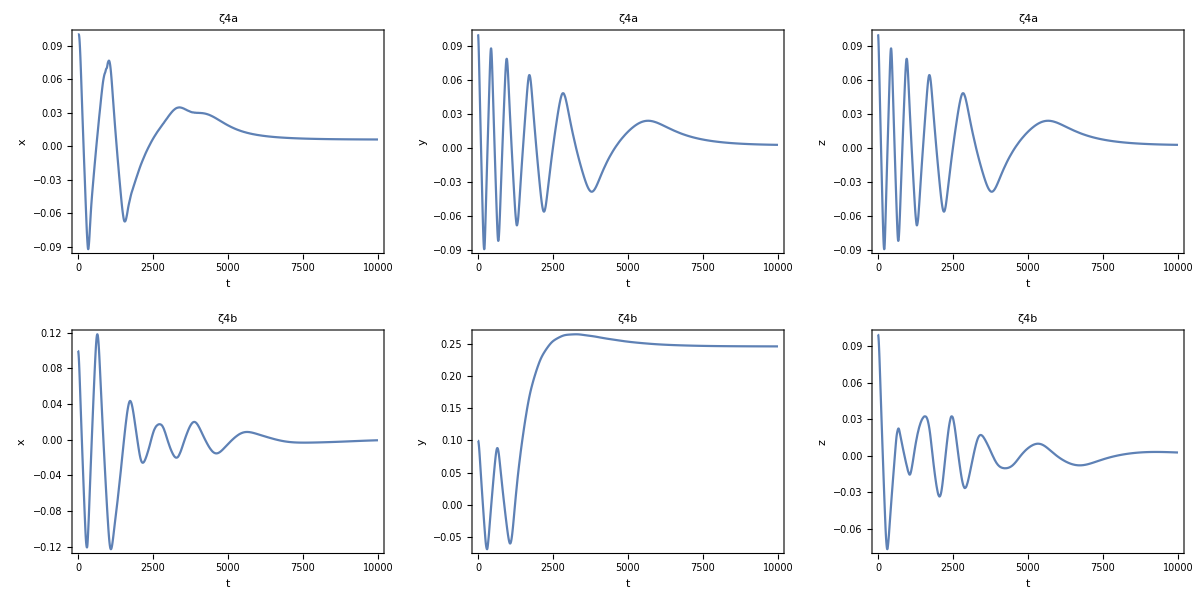

```mathematica
TableForm[{{Plot[solns1[[1]][t],{t,0,Tmax},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["x",Black,14]},PlotLabel->Style["ζ4a",Black,20],Frame->True],
Plot[solns1[[2]][t],{t,0,Tmax},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["y",Black,14]},PlotLabel->Style["ζ4a",Black,20],Frame->True],
Plot[solns1[[3]][t],{t,0,Tmax},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["z",Black,14]},PlotLabel->Style["ζ4a",Black,20],Frame->True]},{
Plot[solns2[[1]][t],{t,0,Tmax},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["x",Black,14]},PlotLabel->Style["ζ4b",Black,20],Frame->True],
Plot[solns2[[2]][t],{t,0,Tmax},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["y",Black,14]},PlotLabel->Style["ζ4b",Black,20],Frame->True],
Plot[solns2[[3]][t],{t,0,Tmax},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["z",Black,14]},PlotLabel->Style["ζ4b",Black,20],Frame->True]}}]
```

```mathematica
TableForm[{ParametricPlot3D[{solns1[[1]][t],solns1[[2]][t],solns1[[3]][t]},{t,0,Tmax},PlotRange->All],
ParametricPlot3D[{solns2[[1]][t],solns2[[2]][t],solns2[[3]][t]},{t,0,Tmax},PlotRange->All]}]
```

-Graphics3D-
-Graphics3D-